# Mathematica Notebook for Problem Set 3

## Stability Diagram: Example 1

Bifurcations occur when f(x) = 0 and f'(x) = 0 simultaneously (they occur at non-hyperbolic fixed points).
With two equations ({f(x)=0, f'(x) = 0}) that are simultaneously true, we can solve for two of the unknowns (for the example below, those are two of x, a,  or r.

Below, I solve for each unknown in terms of the other two.

Notice that I catch two solutions solving for x and r in terms of a.  The x -> 0 solution where r-> 0 and a is free doesn't appear in the other lines...

```mathematica
f[x_,r_,a_]:= r x -a x^2- x^3;
bifurcations = Solve[{f[x,r,a]==0,D[f[x,r,a],x]==0},{x,r}]
bifurcations = Solve[{f[x,r,a]==0,D[f[x,r,a],x]==0},{x,a}]
bifurcations = Solve[{f[x,r,a]==0,D[f[x,r,a],x]==0},{r,a}]
```

{{x→0,r→0},{x→-a/2,r→-a^2/4}}

{{x→-ⅈ √r,a→2 ⅈ √r},{x→ⅈ √r,a→-2 ⅈ √r}}

{{r→-x^2,a→-2 x}}

Version 1:  I plot the solution curves (of r) that I find in the first line:
bifurcations = Solve[{f[x,r,a]==0,D[f[x,r,a],x]==0},{x,r}]

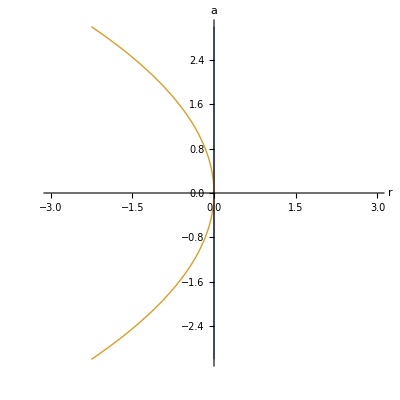

```mathematica
ContourPlot[{r==0, r == -a^2/4},{r,-3,3},{a,-3,3}, Frame->False,Axes->True,AxesLabel->{r,a},ContourStyle->Thick]
```

Version 2: I plot the r = 0 curve using ContourPlot.  I plot the second curve using the solution to 
bifurcations = Solve[{f[x,r,a]==0,D[f[x,r,a],x]==0},{r,a}]

I have r = -x^2 and a = -2x as one of the curves.  Using ParametricPlot, as I vary x the plotting command plots the (r,a) values associated with that specific x.  This traces out the parabola.

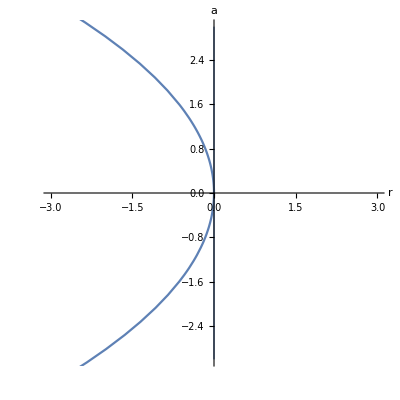

```mathematica
cp = ContourPlot[{r==0},{r,-3,3},{a,-3,3}, Frame->False,Axes->True,AxesLabel->{r,a},ContourStyle->Thick];
pp = ParametricPlot[{-x^2, -2x},{x,-3,3}];
Show[cp,pp]
```

## Stability diagram: Example 2

```mathematica
f[x_, r_, h_] := h + r x - x^3;
bifurcations1 = Solve[{f[x, r, h] == 0, D[f[x, r, h],x] == 0}, {x, r}]
bifurcations2= Solve[{f[x, r, h] == 0, D[f[x, r, h],x] == 0}, {x, h}]
bifurcations3 = Solve[{f[x, r, h] == 0, D[f[x, r, h],x] == 0}, {h, r}]
```

{{x→(-1/2)^(1/3) h^(1/3),r→3 (-1/2)^(2/3) h^(2/3)},{x→-h^(1/3)/2^(1/3),r→(3 h^(2/3))/2^(2/3)},{x→-((-1)^(2/3) h^(1/3))/2^(1/3),r→-(3 (-1)^(1/3) h^(2/3))/2^(2/3)}}

{{x→-(√r)/(√3),h→(2 r^(3/2))/(3 √3)},{x→(√r)/(√3),h→-(2 r^(3/2))/(3 √3)}}

{{h→-2 x^3,r→3 x^2}}

Notice that in all of the solutions above, x depends on the values of the parameters (so x won't stay at a single point as the parameter evolves, each parameter set will have a different fixed point location associated with it).
In this case, using ParametricPlot will catch all of the bifurcation curves.

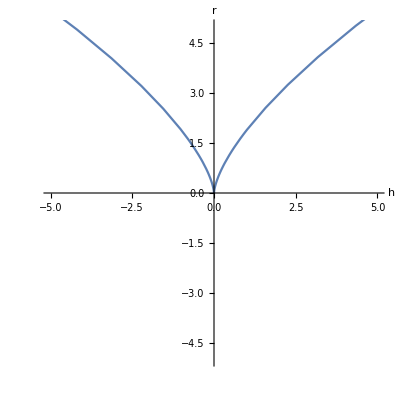

```mathematica
ParametricPlot[{h/.bifurcations3[[1]],r/.bifurcations3[[1]]},{x,-3,3},AxesLabel->{h, r},PlotRange->{{-5,5},{-5,5}}]
```

```mathematica
ParametricPlot[{-2x^3,3x^2},{x,-3,3},AxesLabel->{h, r},PlotRange->{{-5,5},{-5,5}}]
```

-Graphics-

## The cusp-catastrophe surface plotted in 3-space

There are several ways to plot the bifurcation surface. Perhaps the easiest is to use a 3D contour plot.

```mathematica
f[x_, r_, h_] := h + r x - x^3;
ContourPlot3D[f[x,r,h] == 0, {h, -15, 15}, {r, -10, 10}, {x, -10,10}, AxesLabel -> {h, r, x}, ContourStyle -> Opacity[0.8]]
```

-Graphics3D-

Because the equation f(x,r,h)=0 can be rewritten to write h=g(x,r) we can also easily use a 3D Plot or 3D Parametric Plot; however, the surfaces don’t look as nice (even though they are the same!).

```mathematica
ParametricPlot3D[{-r*x+x^3,r,x}, {r, -15,15}, {x, -3,3}, AxesLabel -> {h, r, x},BoxRatios->{1,1/2,1/4}]
```

-Graphics3D-

```mathematica
Plot3D[-r*x+x^3, {r, -15,15}, {x, -3,3},BoxRatios->{1,1/4,1/2}, AxesLabel -> {r, x,h}]
```

-Graphics3D-

## Eigenvalues and Eigenvectors

Mathematica can compute the eigenvalues and eigenvectors for systems with unknown parameters.  Use Eigensystem to get the eigenvalues with their associated eigenvectors.

```mathematica
Eigensystem[{{-1,5},{x,-1}}]
```

{{-1-√5 √x,-1+√5 √x},{{-(√5)/(√x),1},{(√5)/(√x),1}}}

Alternatively you can use Eigenvalue and Eigenvector, although there’s no guarantee between the correspondence of the separate lists

```mathematica
Eigenvalues[{{-1,5},{x,-1}}]
Eigenvectors[{{-1,5},{x,-1}}]
```

{-1-√5 √x,-1+√5 √x}

{{-(√5)/(√x),1},{(√5)/(√x),1}}

## Phase Portraits

Use StreamPlot to plot trajectories.

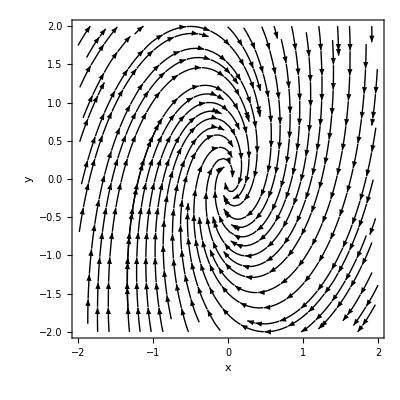

```mathematica
plotsave = StreamPlot[{-x+y,-4x-y},{x,-2,2},{y,-2,2},StreamColorFunction->None,StreamStyle->Black,FrameLabel->{x,y},BaseStyle->Directive[12]]
```

Use Show to plot lines on top of your phase portraits.

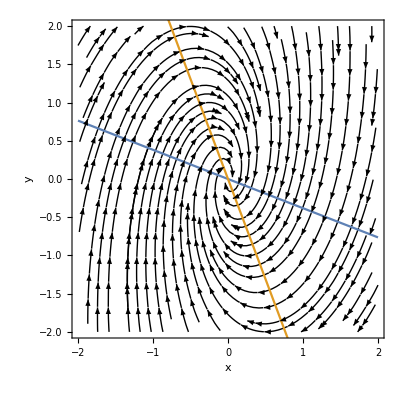

```mathematica
Show[plotsave,
Plot[{1/2 (-3+√5)x,1/2 (-3-√5)x},{x,-2,2}]]
```

Add fixed points (there is just one at the origin, and it is stable).  Use a disk for a stable fixed point and a circle for an unstable one.

```mathematica
?Circle 
(*not filled*)
?Disk 
(*filled*)
```

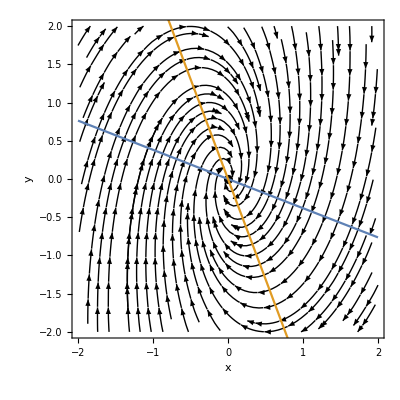

```mathematica
plotfinal = Show[plotsave,Graphics[Disk[{0,0},0.06]],
Plot[{1/2 (-3+√5)x,1/2 (-3-√5)x},{x,-2,2}]]
```

Export the plot

```mathematica
Export["PS03_plot.png",plotfinal]
```